## Electron Scattering

### Calculating Normalization Constant

```mathematica
Clear["Global`*"]
```

Constants

```mathematica
R=6.63
a=0.45
Z=79
hbarc=197.327 (* MeV*fm *)
En1= 126 (* MeV *)
En2=183
econst=18.095 (* e^2/ε0 MeV*fm *)
```

6.63

0.45

79

197.327

126

183

18.095

Charge Density Distribution Form

```mathematica
ρch[r_, ρ0_]:=ρ0/(1+Exp[(r-R)/a])
```

Normalization

```mathematica
(* Triple integral using spherical coordinates *)
```

```mathematica
Int=Integrate[ρch[r, ρ0]*r^2*Sin[theta], {r, 0, Infinity},
{theta, 0, Pi}, {phi, 0, 2*Pi}] 

eq1=Int==Z (* Z of Au *)
ρ0val=Solve[eq1, ρ0] (* Calculating ρ0ch value *)
```

1276.26 ρ0

1276.26 ρ0==79

{{ρ0→0.0618996}}

Charge Density Distribution with specific ρ0

```mathematica
ρ0sol=ρ0/. First[ρ0val]
```

0.0618996

```mathematica
ρch[r_]:=ρ0sol/(1+Exp[(r-R)/a])
```

### Calculating main integral

```mathematica
integrand2=Exp[I*q*r*Cos[theta]]*Sin[theta]
int2=Integrate[integrand2, {theta, 0, Pi}]

(*Integrating using spherical coordinates *)
(* q//z *)
(*tripleIntegral=Integrate[integrand,{r,0,10},{theta,0,Pi},{phi,0,2*Pi}]


simplifiedResult=Simplify[tripleIntegral] *)
```

ⅇ^(ⅈ q r Cos[theta]) Sin[theta]

(2 Sin[q r])/(q r)

```mathematica
integrand3=2*Pi*(r^2)*ρch[r]*(2*Sin[q*r])/(q*r)
int3=Integrate[integrand3, {r, 0, 10}]
simplifiedResult=Simplify[int3]
```

(0.777853 r Sin[q r])/((1+ⅇ^(2.22222 (-6.63+r))) q)

1/q^3 1.94761×10^6 ((0.-1.99694×10^-7 ⅈ) HypergeometricPFQ[{1.,(0.+0. ⅈ)-(0.+0.45 ⅈ) q,(0.+0. ⅈ)-(0.+0.45 ⅈ) q},{1.-(0.+0.45 ⅈ) q,1.-(0.+0.45 ⅈ) q},-3.99388×10^-7]+ⅇ^((0.-10. ⅈ) q) (-1.99694×10^-6 q Hypergeometric2F1[1.,(0.+0. ⅈ)-(0.+0.45 ⅈ) q,1.-(0.+0.45 ⅈ) q,-1788.06]+(0.+1.99694×10^-7 ⅈ) HypergeometricPFQ[{1.,(0.+0. ⅈ)-(0.+0.45 ⅈ) q,(0.+0. ⅈ)-(0.+0.45 ⅈ) q},{1.-(0.+0.45 ⅈ) q,1.-(0.+0.45 ⅈ) q},-1788.06]+ⅇ^((0.+20. ⅈ) q) (-1.99694×10^-6 q Hypergeometric2F1[1.,(0.+0. ⅈ)+(0.+0.45 ⅈ) q,1.+(0.+0.45 ⅈ) q,-1788.06]-(0.+1.99694×10^-7 ⅈ) HypergeometricPFQ[{1.,(0.+0. ⅈ)+(0.+0.45 ⅈ) q,(0.+0. ⅈ)+(0.+0.45 ⅈ) q},{1.+(0.+0.45 ⅈ) q,1.+(0.+0.45 ⅈ) q},-1788.06]))+(0.+1.99694×10^-7 ⅈ) HypergeometricPFQ[{1.,(0.+0. ⅈ)+(0.+0.45 ⅈ) q,(0.+0. ⅈ)+(0.+0.45 ⅈ) q},{1.+(0.+0.45 ⅈ) q,1.+(0.+0.45 ⅈ) q},-3.99388×10^-7])

1/q^3 1.94761×10^6 ((0.-1.99694×10^-7 ⅈ) HypergeometricPFQ[{1.,(0.+0. ⅈ)-(0.+0.45 ⅈ) q,(0.+0. ⅈ)-(0.+0.45 ⅈ) q},{1.-(0.+0.45 ⅈ) q,1.-(0.+0.45 ⅈ) q},-3.99388×10^-7]+ⅇ^((0.-10. ⅈ) q) (-1.99694×10^-6 q Hypergeometric2F1[1.,(0.+0. ⅈ)-(0.+0.45 ⅈ) q,1.-(0.+0.45 ⅈ) q,-1788.06]+(0.+1.99694×10^-7 ⅈ) HypergeometricPFQ[{1.,(0.+0. ⅈ)-(0.+0.45 ⅈ) q,(0.+0. ⅈ)-(0.+0.45 ⅈ) q},{1.-(0.+0.45 ⅈ) q,1.-(0.+0.45 ⅈ) q},-1788.06]+ⅇ^((0.+20. ⅈ) q) (-1.99694×10^-6 q Hypergeometric2F1[1.,(0.+0. ⅈ)+(0.+0.45 ⅈ) q,1.+(0.+0.45 ⅈ) q,-1788.06]-(0.+1.99694×10^-7 ⅈ) HypergeometricPFQ[{1.,(0.+0. ⅈ)+(0.+0.45 ⅈ) q,(0.+0. ⅈ)+(0.+0.45 ⅈ) q},{1.+(0.+0.45 ⅈ) q,1.+(0.+0.45 ⅈ) q},-1788.06]))+(0.+1.99694×10^-7 ⅈ) HypergeometricPFQ[{1.,(0.+0. ⅈ)+(0.+0.45 ⅈ) q,(0.+0. ⅈ)+(0.+0.45 ⅈ) q},{1.+(0.+0.45 ⅈ) q,1.+(0.+0.45 ⅈ) q},-3.99388×10^-7])

### Calculating dσ/dΩ for En=126 & 183 MeV for a range of angle values

```mathematica
(* Defining q(x) for 2 different energies *)
```

```mathematica
q[En_,x_]=(2*En)(Sin[x Degree/2])/hbarc
```

0.0101355 En Sin[(° x)/2]

```mathematica
(* Angle values in degrees *)
```

```mathematica
xValues=Range[10,150,10];

(*Calculating dσdΩ for each x*)

(* Initializing arrays to store values *)
int3Values1={};
int3Values2={};
dσdΩValues1={};
dσdΩValues2={};

For[i=1,i<=Length[xValues],i++,
(*q for current x and En1 *)
qValue1=q[En1,xValues[[i]]];
(*Substituting q into int3 to get int3Value for current x and En1 *)int3Value1=Re[int3/. q->qValue1];
AppendTo[int3Values1,int3Value1];
(*Calculating dσ/dΩ for current x, int3Value and En1 *)
dσdΩValue1=((En1/(2*Pi))^2)*((1/(hbarc))^4)*(econst^2)*((1/qValue1)^4)*(int3Value1^2);
(*Appending values to list*)
AppendTo[dσdΩValues1,dσdΩValue1];


(*q for current x and En2 *)
qValue2=q[En2,xValues[[i]]];
(*Substituting q into int3 to get int3Value for current x and En2 *)int3Value2=Re[int3/. q->qValue2];
AppendTo[int3Values2,int3Value2];
(*Calculating dσ/dΩ for current x, int3Value and En2 *)
dσdΩValue2=((En2/(2*Pi))^2)*((1/(hbarc))^4)*(econst^2)*((1/qValue2)^4)*(int3Value2^2);
(*Appending values to list*)
AppendTo[dσdΩValues2,dσdΩValue2];
]

(* Displaying results *)TableForm[Transpose[{xValues,dσdΩValues1,dσdΩValues2}],TableHeadings->{None,{"x (degrees)","dσdΩ (126 MeV)","dσdΩ (183 MeV)"}}]
```

x (degrees) | dσdΩ (126 MeV) | dσdΩ (183 MeV)
10 | 3126.51 | 1292.74
20 | 136.831 | 36.0299
30 | 14.47 | 1.43928
40 | 1.7429 | 0.00718644
50 | 0.155607 | 0.011332
60 | 0.0024894 | 0.00542254
70 | 0.00341043 | 0.000449562
80 | 0.00539655 | 0.0000388188
90 | 0.00330128 | 0.000157686
100 | 0.00130636 | 0.0000884228
110 | 0.000344314 | 0.0000195918
120 | 0.0000423219 | 4.49669×10^-7
130 | 7.02679×10^-7 | 1.98913×10^-6
140 | 0.0000240916 | 5.19929×10^-6
150 | 0.0000485134 | 6.22308×10^-6

### Creating Scatter plot of dσ/dΩ vs scattering angle x

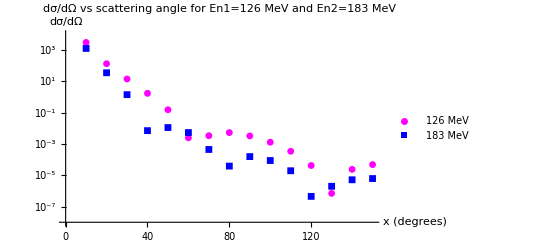

```mathematica
(* dσdΩ vs x scatter plot for both energy levels (semilog) *) scatterPlot=ListPlot[{Transpose[{xValues,dσdΩValues1}],(* En=126 MeV *)Transpose[{xValues,dσdΩValues2}]   (* En=183 MeV *)},PlotLegends->{"126 MeV","183 MeV"},PlotStyle->{Magenta,Blue},PlotMarkers->{Automatic, Small},AxesLabel->{"x (degrees)","dσ/dΩ"},PlotLabel->"dσ/dΩ vs scattering angle for En1=126 MeV and En2=183 MeV",GridLines->Automatic,ScalingFunctions->{None,"Log10"},PlotRange->{Automatic,{10^-8,10000}}];


scatterPlot
```